# The Power of Mathematica

Cameron Devine

St. Martin’s University

## Abstract

This paper is an example of the ease of use and power of Mathematica. In this example Mathematica is used to solve a common differential equations problem and graph the solution. The differences between Matlab and Mathematica and their general merits for students are also discussed.

## Introduction

Several weeks ago I received a take home test where the use of computers was allowed. At that time I had only heard about Mathematica but was interested in its ability to do symbolic math. So against my better judgment I decided download a trial and learn Mathematica while taking the test. Since I have received my scores I can say it wasn’t a horrible idea. For this test I used Mathematica to do symbolic matrix arithmetic and to find differential equation solutions. Finding these solutions by hand can take a very long time and is prone to errors. Using a tool like Mathematica can decrease the risk of errors and automates possibly time consuming calculations.

## Example

### Problem Description

A common differential equations problem is an object connected to a moving surface through a spring and damper in parallel. This system is modeled by the differential equation,

m x''(t)+c x'(t)+k x(t)=f(t),

Where x is the displacement of the object, m is the mass of the object, c is the damping ratio, k is the spring constant, and f(t) is the forcing function. The forcing function is an equation relating time to the force the moving surface is exerting on the spring and damper. For this problem we will consider the forcing function to be,

f(t)=20sin(10t).

This causes the entire differential equation to become,

m x''(t)+c x'(t)+k x(t)=20sin(10t).

Mathematica can be used to solve this equation both symbolically and numerically with values for m, c, and k. For the numeric solution,

m=8, c=10, and k=4.

Solving differential equations does not give a single solution; it gives a set of solutions. To visualize the solutions it can be plotted with multiple initial conditions. In this problem the object starts from rest.

### Symbolic Solution

To solve this differential equation symbolically the DSolve command can be used. This command can solve nth order linear or nonlinear differential equations. The command is used in the following way to solve the differential equation without initial conditions,

```mathematica
solution=DSolve[m*x''[t]+c*x'[t]+k*x[t]==20*Sin[10*t],x[t],t]//Simplify
```

{{x[t]→ⅇ^(-((c+√(c^2-4 k m)) t)/(2 m)) C[1]+ⅇ^(((-c+√(c^2-4 k m)) t)/(2 m)) C[2]-(20 (10 c Cos[10 t]-(k-100 m) Sin[10 t]))/(100 c^2+(k-100 m)^2)}}

While this is the solution it is not a simple answer. This is because the exponents in the solution are the roots of the polynomial with the coefficients of m, c, and k. A simpler solution can be found using the values of m, c, and k.

### Numeric Solution

To find the numeric solution of the differential equation without initial conditions the values of m, c, and k can be set,

```mathematica
m=1; c=4; k=5;
```

The solution can be reevaluated by simply calling it again,

```mathematica
solution
```

{{x[t]→ⅇ^((-2-ⅈ) t) C[1]+ⅇ^((-2+ⅈ) t) C[2]-1/2125 4 (40 Cos[10 t]+95 Sin[10 t])}}

This solution is simpler but also more specific. While this solution is more specific it still has arbitrary constants. To find these arbitrary constants initial conditions are used.

### Initial Condition Solutions

To visualize the solutions to this problem the differential equation can be solved with multiple initial conditions. One initial condition is already defined as,

v(t)=x'(t)=0,

because the object starts at rest. The solution for this differential equation with initial conditions can be found with the following command,

```mathematica
solutions=Table[DSolve[{m*x''[t]+c*x'[t]+k*x[t]==20*Sin[10*t],x'[0]==0,x[0]==d},x[t],t],{d,0,5}];
```

This command creates a list of solutions with different initial conditions. These solutions can now be plotted to visualize several possible solutions,

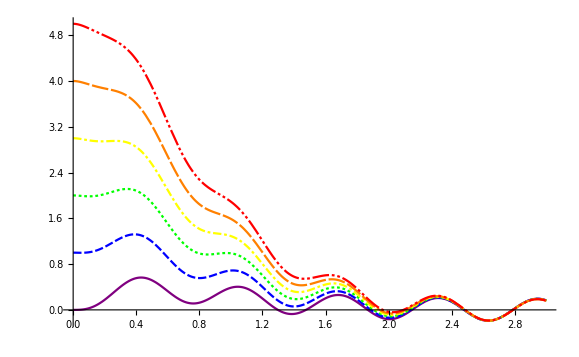

```mathematica
Plot[Evaluate[x[t]/.solutions],{t,0,3},PlotStyle->{Purple,Blue,Green,Yellow,Orange,Red}]
```

This graph shows the displacement starts at the various initial conditions and the specified zero velocity. This response slowly decays to a sign wave. This is because the damper in the system removes all of the energy from the initial conditions. After the energy from the initial conditions is gone the forcing function is the only source of energy.

## Conclusion

Mathematica is useful for almost all mathematical calculations. The number of lines of code to get all the outputs for this example is extremely minimal with only five lines. To simply find the graph in this example would require many more lines in Matlab. In many cases Mathematica is a more useful tool. All simple calculations which can be completed in Matlab can be done in Mathematica. System Dynamics is one field where Matlab is better. This is one of the only fields where Matlab is better. If it was not for the system dynamcis tools in Matlab, Mathematica would be a clear choice. Since many educational institutions already provide Matlab to their students the unique Matlab tools can be used when need and the better tools in Mathematica can be used on personal computers.